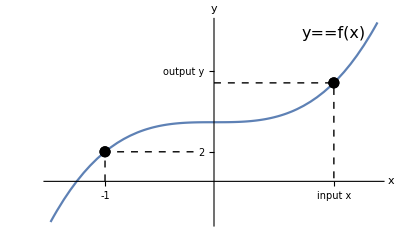

{invcube.pdf,invcube.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=2x^3+4;
Show[
Plot[f[x],{x,-1.5,1.5}],
Graphics[{Black,Dashed,Line[{{-1,0},{-1,2},{-0.15,2}}]}],
Graphics[{Black,Dashed,Line[{{0,f[1.1]},{1.1,f[1.1]},{1.1,0}}]}],
ListPlot[{{-1,f[-1]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1.1,f[1.1]}},PlotStyle->{Black,PointSize[0.02]}],
TicksStyle->Directive[16],
Ticks->{{-1,{1.1,"input\nx"}},{2,{f[1.2],"output\ny"}}},AxesStyle->Directive[16],AxesLabel->{x,y},
Epilog->{Text[Style[HoldForm[y==f[x]],16],{1.1,10}]}
]
Export[{"invcube.pdf","invcube.svg"},%]
```

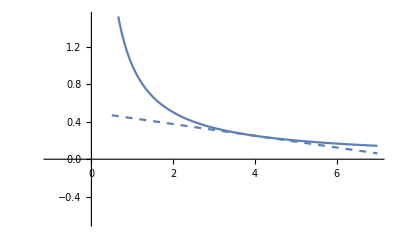

tangentline.png

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Plot[1/x,{x,-1,7},Exclusions->{0}],
Plot[-x/16+1/2,{x,0.5,7},PlotStyle->{Dashed}]
]
Export["tangentline.png",%]
```

```mathematica
D[Sin[x]/(1-Cos[x]),x]//Simplify
```

1/(-1+Cos[x])

```mathematica
Factor[x^2
```

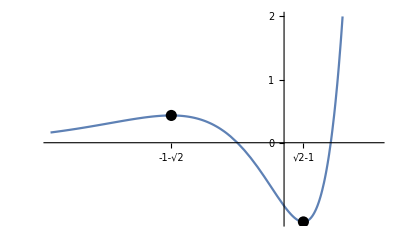

critical.png

```mathematica
f[x_]:=Exp[x](x^2-1)
SetDirectory[NotebookDirectory[]];
Show[
Plot[f[x],{x,-5,2}],
ListPlot[{{-1-Sqrt[2],f[-1-Sqrt[2]]},{-1+Sqrt[2],f[-1+Sqrt[2]]}},PlotStyle->{Black,PointSize[0.02]}],
Ticks->{{-1-Sqrt[2],-1+Sqrt[2]},{0,1,2}}
]
Export["critical.png",%]
```

```mathematica
Integrate[1/(x^2-a^2),x]//TrigToExp
```

Log[1-x/a]/(2 a)-Log[1+x/a]/(2 a)

```mathematica
D[Log[(x-a)/(x+a)]/a/2,x]//Simplify
```

1/(-a^2+x^2)

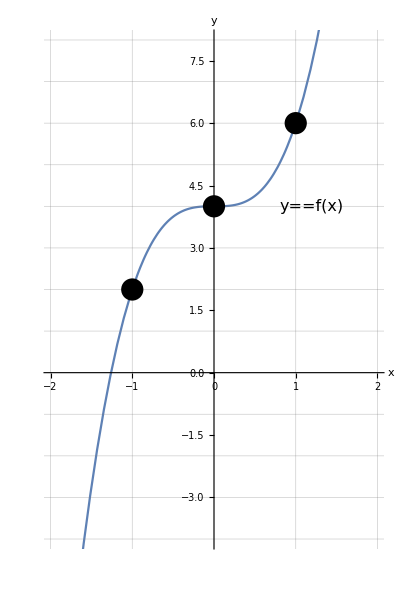

{invcube2.pdf,invcube2.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=2x^3+4;
Show[
Plot[f[x],{x,-2,2}],
ListPlot[{{-1,f[-1]},{1,f[1]},{0,f[0]}},PlotStyle->{Black,PointSize[0.04]}],
(*Graphics[{Black,Dashed,Line[{{-1,0},{-1,2},{-0.15,2}}]}],
Graphics[{Black,Dashed,Line[{{0,f[1.1]},{1.1,f[1.1]},{1.1,0}}]}],
ListPlot[{{-1,f[-1]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1.1,f[1.1]}},PlotStyle->{Black,PointSize[0.02]}],
TicksStyle->Directive[16],
Ticks->{{-1,{1.1,"input\nx"}},{2,{f[1.2],"output\ny"}}},AxesStyle->Directive[16],AxesLabel->{x,y},*)
PlotRange->{{-2,2},{-4,8}},
GridLines->{Range[-2,2],Range[-4,8]},
AspectRatio->1.5,
AxesStyle->Directive[16],AxesLabel->{x,y},
Epilog->{Text[Style[HoldForm[y==f[x]],16],{1.2,4}]}
]
Export[{"invcube2.pdf","invcube2.svg"},%]
```

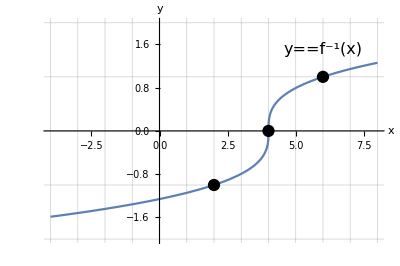

{invcube3.pdf,invcube3.svg}

```mathematica
g[x_]:=CubeRoot[(x-4)/2];
Show[
Plot[g[x],{x,-4,8}],
ListPlot[{{2,g[2]},{6,g[6]},{4,g[4]}},PlotStyle->{Black,PointSize[0.022]}],
(*Graphics[{Black,Dashed,Line[{{-1,0},{-1,2},{-0.15,2}}]}],
Graphics[{Black,Dashed,Line[{{0,f[1.1]},{1.1,f[1.1]},{1.1,0}}]}],

ListPlot[{{1.1,f[1.1]}},PlotStyle->{Black,PointSize[0.02]}],
TicksStyle->Directive[16],
Ticks->{{-1,{1.1,"input\nx"}},{2,{f[1.2],"output\ny"}}},AxesStyle->Directive[16],AxesLabel->{x,y},
*)PlotRange->{{-4,8},{-2,2}},
AxesStyle->Directive[16],AxesLabel->{x,y},
GridLines->{Range[-4,8],Range[-2,2]},
AspectRatio->1/1.5,
Epilog->{Text[Style[HoldForm[y==HoldForm[Superscript[f,-1]][x]],16],{6,1.5}]}
]
Export[{"invcube3.pdf","invcube3.svg"},%]
```

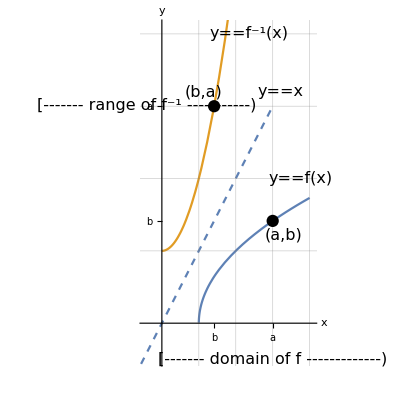

{invgen1.pdf,invgen1.svg}

```mathematica
g[x_]:=Sqrt[x-1];
f[x_]:=Piecewise[{{x^2+1,x>=0}},Indeterminate]
a=3;b=g[a];
Show[
Plot[{g[x],f[x]},{x,-4,4}],
Plot[x,{x,-3,3},PlotStyle->Dashed],
ListPlot[{{a,g[a]},{b,f[b]}},PlotStyle->{Black,PointSize[0.022]}],
PlotRange->{{-0.5,4.1},{-0.5,4.1}},
AxesStyle->Directive[16],AxesLabel->{x,y},
GridLines->{Range[-8,8],Range[-8,9]},
AspectRatio->1,
Ticks->{{{a,HoldForm[a]},{b,HoldForm[b]}},{{a,HoldForm[a]},{b,HoldForm[b]}}},
Epilog->{
Text[Style[HoldForm[y==HoldForm[Superscript[f,-1]][x]],16],{2.35,4}],
Text[Style[HoldForm[y==HoldForm[f][x]],16],{3.75,2}],
Text[Style["(a,b)",16],{a+0.3,b-0.2}],
Text[Style["(b,a)",16],{b-0.3,a+0.2}],
Text[Style[HoldForm[y==x],16],{3.2,3.2}],
Text[Style[Highlighted["[------- domain of f -------------)"],16],{a,-0.5}],
Rotate[Text[Style[Highlighted["[------- range of f^-1 -----------)"],16],{-0.4,b+1.6}],Pi/2]
}
]
Export[{"invgen1.pdf","invgen1.svg"},%]
```

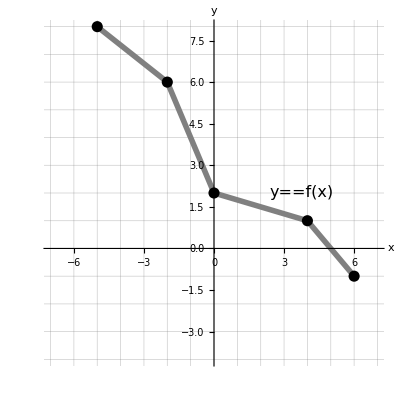

{invgrap1.pdf,invgrap1.svg}

```mathematica
f[x_]:=Piecewise[{{}},Indeterminate]
a=3;b=g[a];
Show[
Plot[{},{x,-10,10}],
Graphics[{Thickness[0.01],Gray,Line[{{-5,8},{-2,6},{0,2},{4,1},{6,-1}}]}],
ListPlot[{{-5,8},{0,2},{-2,6},{4,1},{6,-1}},PlotStyle->{Black,PointSize[0.02]}],
PlotRange->{{-7,7},{-4,8}},
AxesStyle->Directive[16],AxesLabel->{x,y},
GridLines->{Range[-8,8],Range[-8,9]},
AspectRatio->1,
Epilog->{
Text[Style[HoldForm[y==HoldForm[f][x]],16],{3.75,2}],}
]
Export[{"invgrap1.pdf","invgrap1.svg"},%]
```

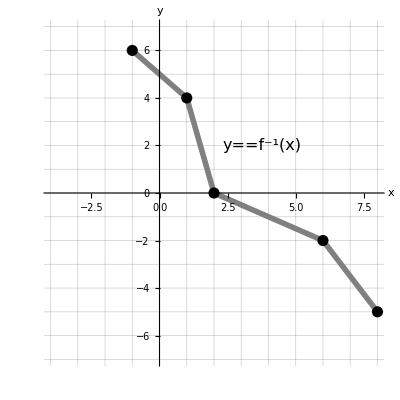

{invgrap2.pdf,invgrap2.svg}

```mathematica
f[x_]:=Piecewise[{{}},Indeterminate]
a=3;b=g[a];
Show[
Plot[{},{x,-10,10}],
Graphics[{Thickness[0.01],Gray,Line[Reverse/@{{-5,8},{-2,6},{0,2},{4,1},{6,-1}}]}],
ListPlot[Reverse/@{{-5,8},{0,2},{-2,6},{4,1},{6,-1}},PlotStyle->{Black,PointSize[0.02]}],
PlotRange->{{-4,8},{-7,7}},
AxesStyle->Directive[16],AxesLabel->{x,y},
GridLines->{Range[-8,8],Range[-8,9]},
AspectRatio->1,
Epilog->{
Text[Style[HoldForm[y==HoldForm[Superscript[f,-1]][x]],16],{3.75,2}],}
]
Export[{"invgrap2.pdf","invgrap2.svg"},%]
```

```mathematica
Reverse/@{{-5,8},{-2,6},{0,2},{4,1},{6,-1}}
```

{{8,-5},{6,-2},{2,0},{1,4},{-1,6}}

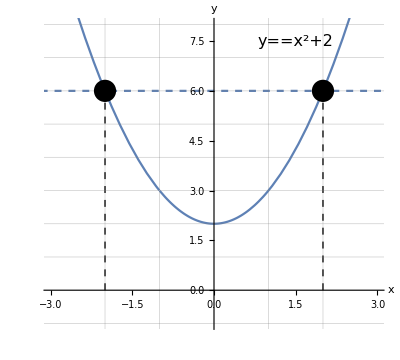

{oneone1.pdf,oneone1.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=x^2+2;
Show[
Plot[f[x],{x,-4,4}],
Plot[6,{x,-4,4},PlotStyle->{Dashed}],
Graphics[{Dashed,Line[{{-2,0},{-2,6}}]}],
Graphics[{Dashed,Line[{{2,0},{2,6}}]}],
ListPlot[{{-2,f[-2]},{2,f[2]}},PlotStyle->{Black,PointSize[0.04]}],
(*Graphics[{Black,Dashed,Line[{{-1,0},{-1,2},{-0.15,2}}]}],
Graphics[{Black,Dashed,Line[{{0,f[1.1]},{1.1,f[1.1]},{1.1,0}}]}],
ListPlot[{{-1,f[-1]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1.1,f[1.1]}},PlotStyle->{Black,PointSize[0.02]}],
TicksStyle->Directive[16],
Ticks->{{-1,{1.1,"input\nx"}},{2,{f[1.2],"output\ny"}}},AxesStyle->Directive[16],AxesLabel->{x,y},*)
PlotRange->{{-3,3},{-1,8}},
GridLines->{Range[-2,2],Range[-4,8]},
AspectRatio->0.9,
AxesStyle->Directive[16],AxesLabel->{x,y},
Epilog->{Text[Style[HoldForm[y==x^2+2],16],{1.5,7.5}]}
]
Export[{"oneone1.pdf","oneone1.svg"},%]
```

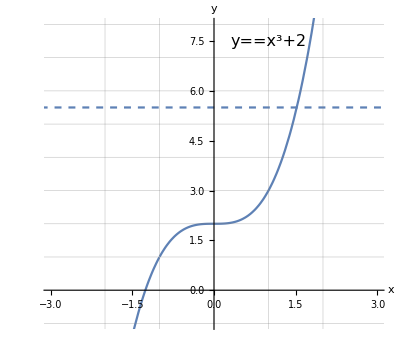

{oneone2.pdf,oneone2.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=x^3+2;
Show[
Plot[f[x],{x,-4,4}],
Plot[5.5,{x,-4,4},PlotStyle->{Dashed}],
ListPlot[{{-2,f[-2]},{2,f[2]}},PlotStyle->{Black,PointSize[0.04]}],
(*Graphics[{Black,Dashed,Line[{{-1,0},{-1,2},{-0.15,2}}]}],
Graphics[{Black,Dashed,Line[{{0,f[1.1]},{1.1,f[1.1]},{1.1,0}}]}],
ListPlot[{{-1,f[-1]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1.1,f[1.1]}},PlotStyle->{Black,PointSize[0.02]}],
TicksStyle->Directive[16],
Ticks->{{-1,{1.1,"input\nx"}},{2,{f[1.2],"output\ny"}}},AxesStyle->Directive[16],AxesLabel->{x,y},*)
PlotRange->{{-3,3},{-1,8}},
GridLines->{Range[-2,2],Range[-4,8]},
AspectRatio->0.9,
AxesStyle->Directive[16],AxesLabel->{x,y},
Epilog->{Text[Style[HoldForm[y==x^3+2],16],{1,7.5}]}
]
Export[{"oneone2.pdf","oneone2.svg"},%]
```

Power::infy: Infinite expression 1/0 encountered.

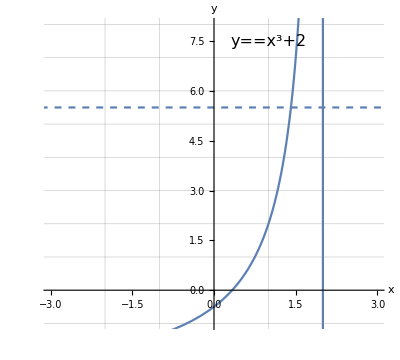

{oneone3.pdf,oneone3.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
f[x_]:=(3x-1)/(2-x);
Show[
Plot[f[x],{x,-4,4}],
Plot[5.5,{x,-4,4},PlotStyle->{Dashed}],
ListPlot[{{-2,f[-2]},{2,f[2]}},PlotStyle->{Black,PointSize[0.04]}],
(*Graphics[{Black,Dashed,Line[{{-1,0},{-1,2},{-0.15,2}}]}],
Graphics[{Black,Dashed,Line[{{0,f[1.1]},{1.1,f[1.1]},{1.1,0}}]}],
ListPlot[{{-1,f[-1]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{1.1,f[1.1]}},PlotStyle->{Black,PointSize[0.02]}],
TicksStyle->Directive[16],
Ticks->{{-1,{1.1,"input\nx"}},{2,{f[1.2],"output\ny"}}},AxesStyle->Directive[16],AxesLabel->{x,y},*)
PlotRange->{{-3,3},{-1,8}},
GridLines->{Range[-2,2],Range[-4,8]},
AspectRatio->0.9,
AxesStyle->Directive[16],AxesLabel->{x,y},
Epilog->{Text[Style[HoldForm[y==x^3+2],16],{1,7.5}]}
]
Export[{"oneone3.pdf","oneone3.svg"},%]
```